```mathematica
Clear["`*"]
```

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

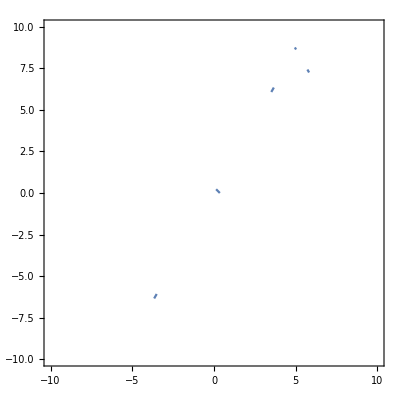

```mathematica
ContourPlot[Sqrt[y]Sqrt[Sqrt[3]x-y]Sqrt[-Sqrt[3](x-10)-y]==0,{x,-10,10},{y,-10,10}]
```

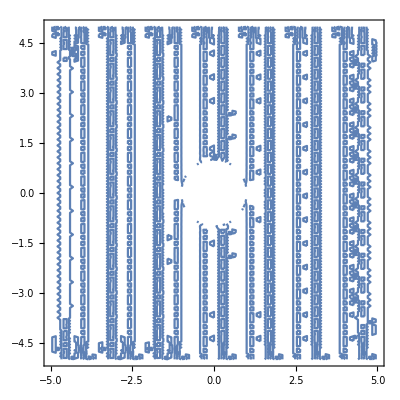

```mathematica
ContourPlot[Sin[99x]Sqrt[x^2+y^2-1]==0,{x,-5,5},{y,-5,5}]
```

```mathematica
1+1
```

2

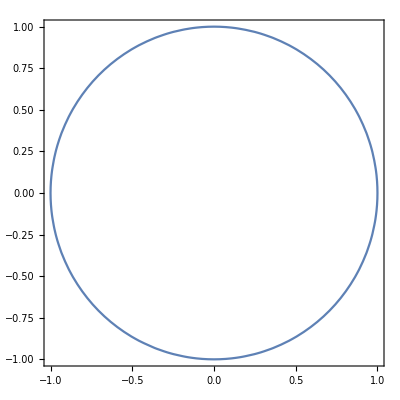

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

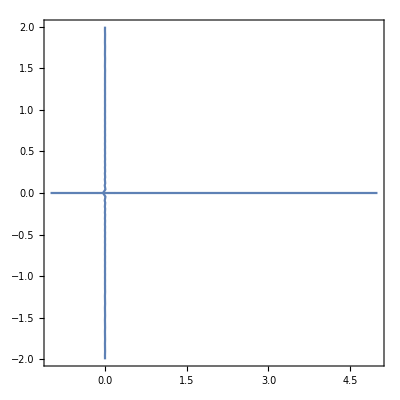

```mathematica
ContourPlot[x y==0,{x,-1,5},{y,-2,2}]
```

```mathematica
ContourPlot[
(x^2+y^2-100)(5Sin[1/5x]-y)Sqrt[(x+0.89)^2+(y+5.49)^2-1.72)^0 Sqrt[(x-9.73];;
]
```

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

2

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

f[x]==x^2

WolframAlphaQueryNoResults

```mathematica
(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^0*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^0*((x - 5.03)^2 + (y + 1.18)^2 - 1.26))
```

(-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) (-y+5 Sin[x/5])

```mathematica
(-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) (-y+5 Sin[x/5])//InputForm
```

(-100 + x^2 + y^2)*(-1.26 + (-5.03 + x)^2 + (1.18 + y)^2)*(-y + 5*Sin[x/5])

```mathematica
((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^0*Sqrt[10 - x]^0
```

-1.26+(4.97+x)^2+(-0.95+y)^2

```mathematica
f[x_,y_]:=((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^0.0001*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^0.0001*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)))(((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^0.0001*Sqrt[10 - x]^0.0001)
```

```mathematica
f[x,y]
```

(10-x)^0.00005 (10+x)^0.00005 (-1.29+(-9.73+x)^2+(-5.4+y)^2)^0.00005 (-1.26+(4.97+x)^2+(-0.95+y)^2) (-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) (-1.72+(9.89+x)^2+(5.49+y)^2)^0.00005 (-y+5 Sin[x/5])

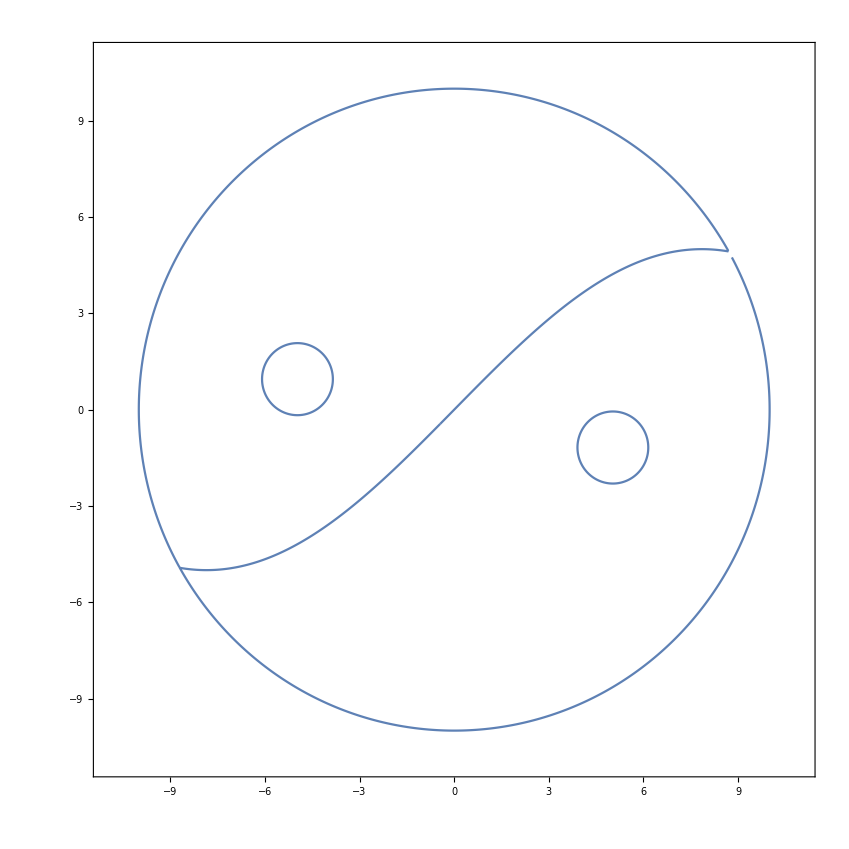

```mathematica
ContourPlot[f[x,y]==0,{x,-11,11},{y,-11,11},MaxRecursion->6]
```

```mathematica
f[x,y]//Simplify[#,Assumptions->{x∈Reals,y∈Reals}]&
```

(100-x^2)^0.00005 (-1.26+(4.97+x)^2+(-0.95+y)^2) (-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) ((-1.29+(-9.73+x)^2+(-5.4+y)^2) (-1.72+(9.89+x)^2+(5.49+y)^2))^0.00005 (-y+5 Sin[x/5])

```mathematica
x^0
```

1

```mathematica
Sqrt[x-1]^0
```

1

```mathematica
Sqrt[2+3ⅈ]//N
```

1.67415+0.895977 ⅈ

WolframAlphaQueryNoResults

```mathematica
(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)
```

(-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) (-y+5 Sin[x/5])

```mathematica
(x + 4.97)^2 + (y - 0.95)^2 - 1.26
```

-1.26+(4.97+x)^2+(-0.95+y)^2

```mathematica
f[x_,y_]:=((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*((x - 5.03)^2 + (y + 1.18)^2 - 1.26))((x + 4.97)^2 + (y - 0.95)^2 - 1.26);
```

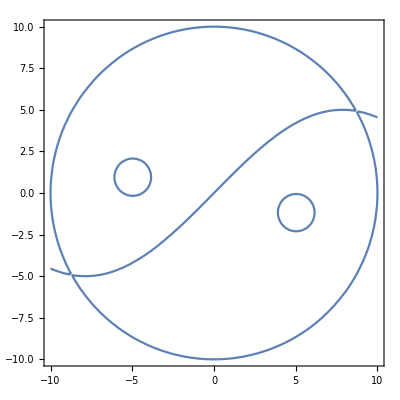

```mathematica
ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10}]
```

```mathematica
Sqrt[x]^0
```

1

WolframAlphaQueryNoResults

```mathematica
(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^1*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^1*((x - 5.03)^2 + (y + 1.18)^2 - 1.26))
```

√(-1.29+(-9.73+x)^2+(-5.4+y)^2) (-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) √(-1.72+(9.89+x)^2+(5.49+y)^2) (-y+5 Sin[x/5])

```mathematica
Sqrt[x + 10]^1*Sqrt[10 - x]
```

√(10-x) √(10+x)

```mathematica
f[x_,y_]:=((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^1*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^1*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)))(Sqrt[x + 10]^1*Sqrt[10 - x]);
```

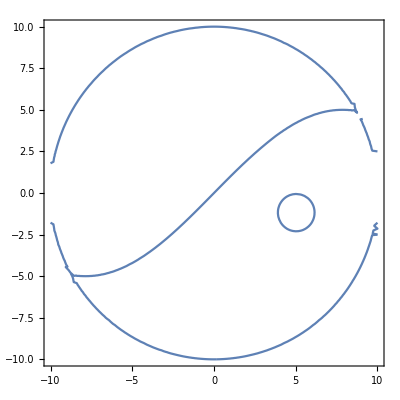

```mathematica
ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10}]
```

WolframAlphaQueryNoResults

```mathematica
(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^1*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^0*((x - 5.03)^2 + (y + 1.18)^2 - 1.26))
```

(-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) √(-1.72+(9.89+x)^2+(5.49+y)^2) (-y+5 Sin[x/5])

```mathematica
((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^1*Sqrt[10 - x]^1
```

√(10-x) √(10+x) (-1.26+(4.97+x)^2+(-0.95+y)^2)

```mathematica
f[x_,y_]:=((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^1*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^1*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)))(((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^1*Sqrt[10 - x]^1);
```

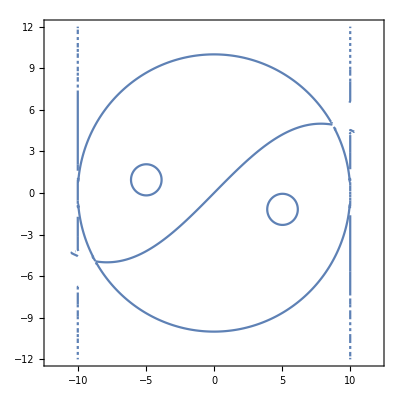

```mathematica
ContourPlot[f[x,y]==0,{x,-12,12},{y,-12,12},MaxRecursion->4]
```

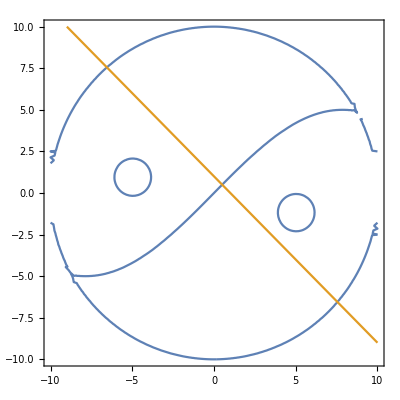

```mathematica
ContourPlot[{f[x,y]==0,x+y==1},{x,-10,10},{y,-10,10}]
```

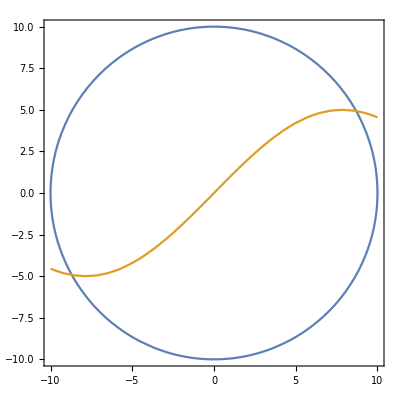

```mathematica
ContourPlot[
{
x^2+y^2-100==0,
5*Sin[(1/5)*x] - y==0,
Sqrt[x + 10]==0,
Sqrt[10 - x]==0
}
,{x,-10,10},{y,-10,10}]
```

```mathematica
Solve[
{
y==√(100-x^2),
5*Sin[(1/5)*x] - y==0
},
{x,y}
]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{y==√(100-x^2),-y+5 Sin[x/5]==0},{x,y}]

```mathematica
Solve[x^2+y^2-100==0,y]
```

{{y→-√(100-x^2)},{y→√(100-x^2)}}

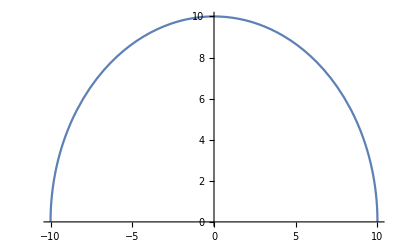

```mathematica
Plot[√(100-x^2),{x,-10,10}]
```

```mathematica
FindRoot[√(100-x^2)==5 Sin[x/5],{x,5}]
FindRoot[-√(100-x^2)==5 Sin[x/5],{x,-5}]
```

{x→8.7012}

{x→-8.7012}

```mathematica
Solve[5*Sin[(1/5)*x] - y==0,y]
```

{{y→5 Sin[x/5]}}

```mathematica
Sqrt[x + 10]^0
```

1

```mathematica
Sqrt[10 - x]^0
```

1

```mathematica
((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^1*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^0*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)))(((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^1*Sqrt[10 - x]^1)
```

√(10-x) √(10+x) (-1.26+(4.97+x)^2+(-0.95+y)^2) (-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) √(-1.72+(9.89+x)^2+(5.49+y)^2) (-y+5 Sin[x/5])

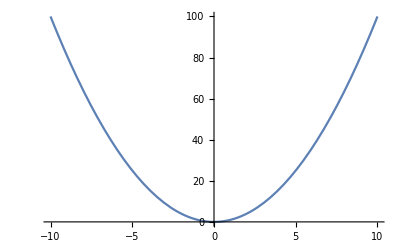

```mathematica
Plot[x^2,{x,-10,10}]
```

```mathematica
f[x_]:=((1/Sqrt[x - 1])*Sqrt[x - 1])
```

```mathematica
f[1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

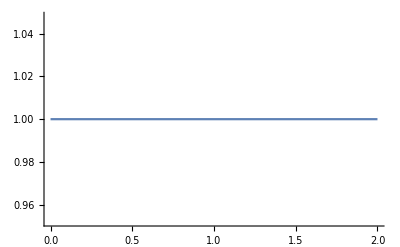

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
1/Sqrt[x-1]*Sqrt[x-1]
```

1

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^2 Sqrt[x-2]^0
```

```mathematica
f[-2]
```

4

```mathematica
Plot[f[x],{x,-10,10}]
```

-Graphics-

```mathematica
Sqrt[-123]
```

ⅈ √123

```mathematica
(ⅈ √123)^0
```

1

```mathematica
f[x_,y_]:=((x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*Sqrt[(x + 9.89)^2 + (y + 5.49)^2 - 1.72]^0.0001*(Sqrt[(x - 9.73)^2 + (y - 5.4)^2 - 1.29]^0.0001*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)))(((x + 4.97)^2 + (y - 0.95)^2 - 1.26)*Sqrt[x + 10]^0.0001*Sqrt[10 - x]^0.0001)
```

```mathematica
r=Solve[f[x,y]==0,y]
```

{{y→-1. √(100.-1. x^2)},{y→√(100.-1. x^2)},{y→0.5 (-10.98-1. √(-384.368-79.12 x-4. x^2))},{y→0.5 (-10.98+√(-384.368-79.12 x-4. x^2))},{y→0.5 (1.9-1. √(-93.7636-39.76 x-4. x^2))},{y→0.5 (1.9+√(-93.7636-39.76 x-4. x^2))},{y→0.5 (-2.36-1. √(-96.1636+40.24 x-4. x^2))},{y→0.5 (-2.36+√(-96.1636+40.24 x-4. x^2))},{y→0.5 (10.8-1. √(-373.532+77.84 x-4. x^2))},{y→0.5 (10.8+√(-373.532+77.84 x-4. x^2))},{y→5. Sin[0.2 x]}}

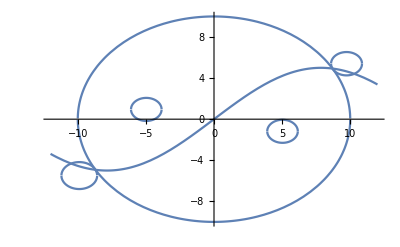

```mathematica
Plot[y/.r,{x,-12,12}]
```

```mathematica
Clear[f];
```

```mathematica
f[x_]=Piecewise[{{□, □}, {Indeterminate, True}}]
```

Piecewise[{{□, □}, {Indeterminate, True}}]

```mathematica
f[x_,y_]:=Sqrt[y]Sqrt[Sqrt[3]x-y]Sqrt[-Sqrt[3](x-10)-y]
```

```mathematica
f[x,y]
```

√(-√3 (-10+x)-y) √(√3 x-y) √y

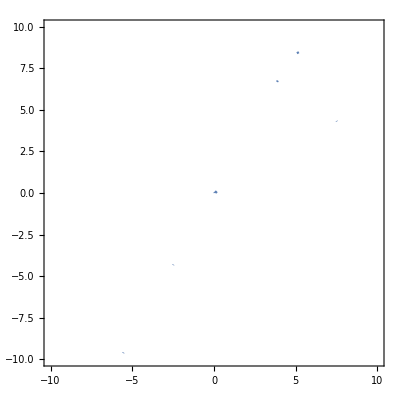

```mathematica
ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10},MaxRecursion->4]
```

```mathematica
(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)*((x + 4.97)^2 + (y - 0.95)^2 - 1.26) == 0
```

(-1.26+(4.97+x)^2+(-0.95+y)^2) (-100+x^2+y^2) (-1.26+(-5.03+x)^2+(1.18+y)^2) (-y+5 Sin[x/5])==0

```mathematica
tjF[x_,y_]:=(x^2 + y^2 - 100)*(5*Sin[(1/5)*x] - y)*((x - 5.03)^2 + (y + 1.18)^2 - 1.26)*((x + 4.97)^2 + (y - 0.95)^2 - 1.26)
```

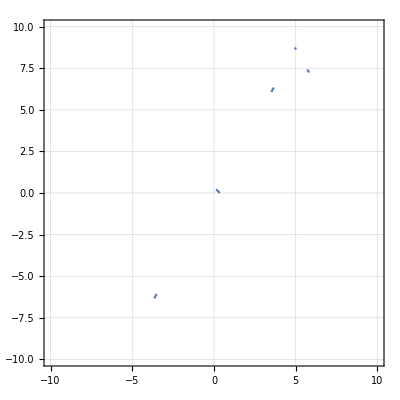

```mathematica
ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10},GridLines->Automatic]
```

```mathematica
(x + 9.89)^2 + (y + 5.49)^2
```

(9.89+x)^2+(5.49+y)^2

```mathematica
Reduce[(x + 9.89)^2 + (y + 5.49)^2>1.72,{},Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

y<-6.80149||(y==-6.80149&&(x<-9.89||x>-9.89))||(-6.80149<y<-4.17851&&(x<-9.89-1.00419×10^-7 √(-2.81833×10^15-1.08885×10^15 y-9.91668×10^13 y^2)||x>-9.89+1.00419×10^-7 √(-2.81833×10^15-1.08885×10^15 y-9.91668×10^13 y^2)))||(y==-4.17851&&(x<-9.89-5.02096×10^-8 ⅈ||x>-9.89-5.02096×10^-8 ⅈ))||y>-4.17851

```mathematica
f[x_,y_]:=(x + 9.89)^2 + (y + 5.49)^2;
f2[x_,y_]:=(x - 9.73)^2 + (y - 5.4)^2 ;
```

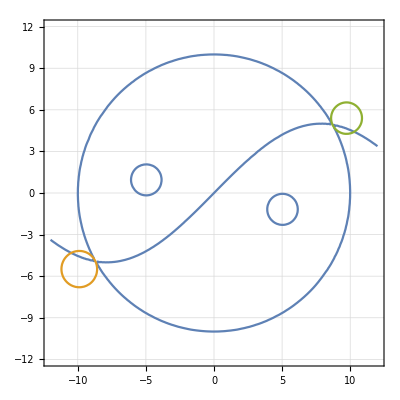

```mathematica
ContourPlot[
{
tjF[x,y]==0,
f[x,y]==1.72,
f2[x,y]==1.29
},
{x,-12,12},
{y,-12,12},
GridLines->Automatic
]
```

```mathematica
ContourPlot[,{x,-12,12},{y,-12,12}]
```

-Graphics-

```mathematica
left=-35;right=35;
```

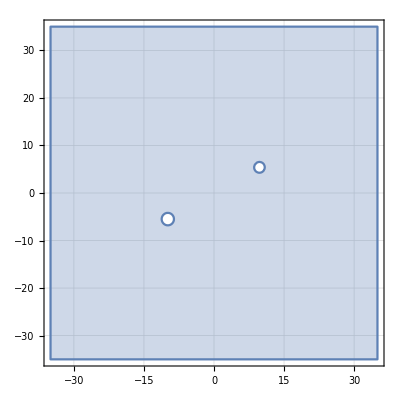

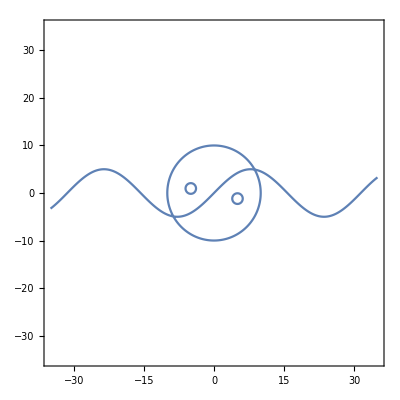

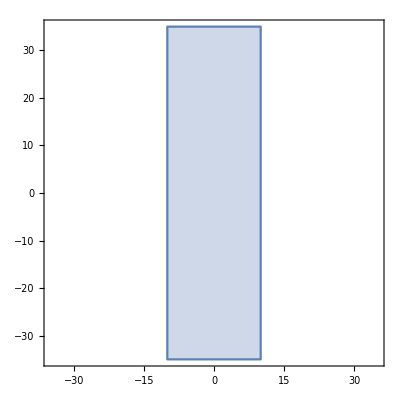

```mathematica
p1=cleanRegionPlot@RegionPlot[{
f[x,y]>1.72&&f2[x,y]>1.29
},{x,left,right},{y,left,right},GridLines->Automatic,MaxRecursion->5]
p2=ContourPlot[tjF[x,y]==0,{x,left,right},{y,left,right},MaxRecursion->5]
p3=cleanRegionPlot@RegionPlot[-10<x<10,{x,left,right},{y,left,right}]
```

```mathematica
Overlay[{p1,p2,p3}]
```

-Graphics--Graphics--Graphics-